```mathematica
tempSys[a_,b_]=
{x'[t]==a x[t]}
```

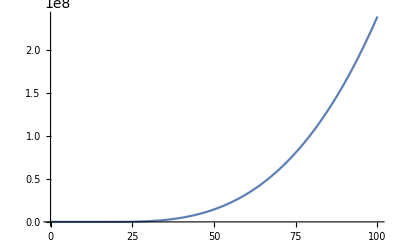

```mathematica
With[{a=0.5,x0= 1},
sol=NDSolve[Join[{tempSys[a,b],x[0]==x0}],{x[t]},{t,0,20}]];
Plot[x[t]/.sol,{t,0,100}]
```

```mathematica
equsICU[a1_,a2_,a3_,a4_,a5_,μ_] = 
{c'[t]==a1 c[t] - a2 q[t],
q'[t] == a2 q[t],
w'[t] == a3 c[t] - μ a4 w[t] + (1-μ)a5 w[t]};
```

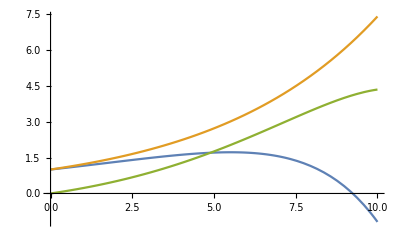

```mathematica
With[{a1=0.35,a2=0.2,a3=0.2,a4=0.3,a5 = 0.1,μ=0.001,tMax=10, c0 = 1,q0 = 1,w0 = 0},
sol= NDSolve[Join[{equs[a1,a2,a3,a4,a5,μ], c[0] == c0,q[0]==q0,w[0]==w0}],{c[t],q[t],w[t]},{t,0,10}];
Plot[Evaluate[{c[t],q[t],w[t]}/.sol],{t,0,tMax}]]
```

```mathematica
Manipulate[
solICU= NDSolve[Join[{equsICU[a1,a2,a3,a4,a5,μ], c[0] == c0,q[0]==q0,w[0]==w0}],{c[t],q[t],w[t]},{t,0,tMax}];
Plot[Evaluate[{c[t],q[t],w[t]}/.solICU],{t,0,tMax}],
{{a1,0.1},0,2},{{a2,0.2},0,2},{{a3,0.15},0,2},{{a4,0.25},0,2},{{a5,0.125},0,2},
{{c0,1},0,10},{q0,0,10},{w0,0,10},{μ,0,1},
{{tMax,1},0,3000}]
```

```mathematica
equsICU = 
{w'[t]==b1 c-μ1 w[t]-η1 w[t]-b2 w[t],
icu'[t]==b2 w[t]-μ2 icu[t]-η2 icu[t],
d'[t]==μ1 w[t]+μ2 icu[t],
r'[t]==η1 w[t]+η2 icu[t]};
```

```mathematica
solsAnalytic=DSolve[equsICU,{w[t],icu[t],d[t],r[t]},t];
```

```mathematica
solsAnalytic[[1,4]]
```

w[t]→(b1 c ⅇ^(t (-b2-η1-μ1)+t (b2+η1+μ1)))/(b2+η1+μ1)+ⅇ^(t (-b2-η1-μ1)) C[4]